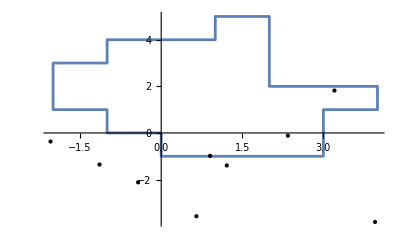

```mathematica
Show[ListLinePlot[{{0.0,0.0},{-1.0,0.0},{-1.0,1.0},{-2.0,1.0},{-2.0,3.0},{-1.0,3.0},{-1.0,4.0},{1.0,4.0},{1.0,5.0},{2.0,5.0},{2.0,2.0},{4.0,2.0},{4.0,1.0},{3.0,1.0},{3.0,-1.0},{0.0,-1.0},{0,0}}],Graphics[Point[{{3.9545897134921857,-3.8182027930403839},
{2.3434184203490060,-0.1163495789476965},
{1.2128949158717504,-1.3965614086181022},
{-2.0467389628672130,-0.3693196193239627},
{0.6510680387153283,-3.5763469180162337},
{0.9037014478472933,-0.9849844922751192},
{3.2043577608204385 ,1.8196222483974553},
{-0.4266652850111763,-2.1200910457371434},
{-1.1403662468827154,-1.3541692830885195}
}]],PlotRange->All]
```

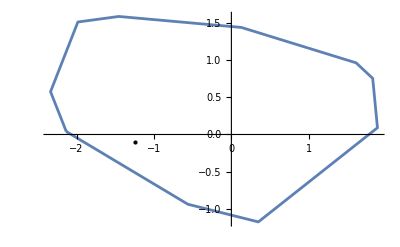

```mathematica
Show[ListLinePlot[{
{-2.1319195442383808 ,0.0395409033987223},
       {-0.5621095131454022,-0.9365507736928824},
{0.3485746254610677,-1.1736402918368476},
{1.8863744780712486 ,0.0907817953769384},
{1.8249538458925848 ,0.7536750469958836},
{1.6104523706340535 ,0.9621928088110658},
{0.1287346897263454 ,1.4375656396154796},
{-1.4537268736154378 ,1.5848375829047325},
{-1.9824414441850776 ,1.5104065626161348},
{-2.3353247296984637 ,0.5746456126824404},
{-2.1319195442383808 ,0.0395409033987223}
}],
Graphics[Point[{
{-1.2416643090442676,-0.0984003403910210}
}
]],PlotRange->All]
```

```mathematica
area[pts_]:=1/2 Abs[Sum[Det[{{pts[[i,1]],pts[[i,2]]},{pts[[i+1,1]],pts[[i+1,2]]}}],{i,1,Length[pts]-1}]+Det[{{pts[[Length[pts],1]],pts[[Length[pts],2]]},{pts[[1,1]],pts[[1,2]]}}]]
SumzOfArea[vtx_,pt_]:=Module[{areas,totalArea},areas=Table[area[{vtx[[i]],pt,vtx[[i+1]]}],{i,1,Length[vtx]-1}];
totalArea=Total[Append[areas,area[{vtx[[Length[vtx]]],pt,vtx[[1]]}]]];totalArea==area[vtx]]

allNonNegativeQ[list_]:=AllTrue[list,#>=0&]
orientation[vtx_,pt_]:=Module[{list},
list=Table[(vtx[[i+1,1]]-vtx[[i,1]]) (pt[[2]]-vtx[[i,2]])-(pt[[1]]-vtx[[i,1]]) (vtx[[i+1,2]]-vtx[[i,2]]),{i,1,Length[vtx]-1}];
list=Append[list,(vtx[[1,1]]-vtx[[Length[vtx],1]]) (pt[[2]]-vtx[[Length[vtx],2]])-(pt[[1]]-vtx[[Length[vtx],1]]) (vtx[[1,2]]-vtx[[Length[vtx],2]])];If[allNonNegativeQ[list],True,False]]


Gridd[x0_,y0_,h_]:=Module[{grid},grid=<|"x0"->x0,"y0"->y0,"h"->h|>;
grid["get_cell"]=Function[{x,y},{Floor[(x-x0)/h],Floor[(y-y0)/h]}];
grid["get_cells"]=Function[{x,y},Module[{i,j,cells},
i=Floor[(x-x0)/h];
j=Floor[(y-y0)/h];
cells={};
If[((x-x0)/h==Floor[(x-x0)/h])&&((y-y0)/h==Floor[(y-y0)/h]),
AppendTo[cells,{i-1,j}];
AppendTo[cells,{i-1,j-1}];
AppendTo[cells,{i,j-1}];,
If[((x-x0)/h==Floor[(x-x0)/h]),
AppendTo[cells,{i-1,j}]];,
If[((y-y0)/h==Floor[(y-y0)/h]),AppendTo[cells,{i,j-1}],Nothing]];
AppendTo[cells,{i,j}];
cells]];
grid["get_cell_center"]=Function[{i,j},{x0+(i+0.5)*h,y0+(j+0.5)*h}];grid]

isOnLine[{p1_,p2_},q_]:=Min[p1[[1]],p2[[1]]]<=q[[1]]<=Max[p1[[1]],p2[[1]]]&&Min[p1[[2]],p2[[2]]]<=q[[2]]<=Max[p1[[2]],p2[[2]]];
doIntersect[{p1_,q1_},{p2_,q2_}]:=Module[{d1,d2,d3,d4},d1=(q1[[1]]-p1[[1]]) (p2[[2]]-p1[[2]])-(q1[[2]]-p1[[2]]) (p2[[1]]-p1[[1]]);
d2=(q1[[1]]-p1[[1]]) (q2[[2]]-p1[[2]])-(q1[[2]]-p1[[2]]) (q2[[1]]-p1[[1]]);
d3=(q2[[1]]-p2[[1]]) (p1[[2]]-p2[[2]])-(q2[[2]]-p2[[2]]) (p1[[1]]-p2[[1]]);
d4=(q2[[1]]-p2[[1]]) (q1[[2]]-p2[[2]])-(q2[[2]]-p2[[2]]) (q1[[1]]-p2[[1]]);
(((d1<0&&d2>0)||(d1>0&&d2<0))&&((d3<0&&d4>0)||(d3>0&&d4<0)))||(d1==0&&isOnLine[{p1,q1},p2])||(d2==0&&isOnLine[{p1,q1},q2])||(d3==0&&isOnLine[{p2,q2},p1])||(d4==0&&isOnLine[{p2,q2},q1])]

isPointInside[polygon_,q_]:=Module[{n,extreme,count,i},n=Length[polygon];
If[n<3,Return[False]];
extreme={10^10,q[[2]]};count=0;
i=1;
While[i<=n,If[doIntersect[{polygon[[i]],polygon[[Mod[i,n]+1]]},{q,extreme}],If[isOnLine[{polygon[[i]],polygon[[Mod[i,n]+1]]},q],Return[True]];
count++;];
i++;];
OddQ[count]]

getPolygonCells[grid_,vertices_]:=Module[{minX,minY,maxX,maxY,minCell,maxCell,polygonCells,i,j},If[Length[vertices]==0,Return[{}]];
minX=Min[vertices[[All,1]]];
minY=Min[vertices[[All,2]]];
maxX=Max[vertices[[All,1]]];
maxY=Max[vertices[[All,2]]];
minCell=grid["get_cell"][minX,minY];
maxCell=grid["get_cell"][maxX,maxY];
polygonCells={};
Do[Do[If[isPointInside[vertices,grid["get_cell_center"][i,j]],AppendTo[polygonCells,{i,j}]],{j,minCell[[2]],maxCell[[2]]}],{i,minCell[[1]],maxCell[[1]]}];
DeleteDuplicates[Sort[polygonCells]]]

gridMethod[grid_,polygonCells_,point_]:=Module[{cells,found=inside},cells=grid["get_cells"][point[[1]],point[[2]]];
Do[If[MemberQ[polygonCells,cell],inside=True],{cell,cells}];inside]
```

```mathematica
(*Нужно ввести свой путь к данным*)
```

```mathematica
Clear[data10,data100,Data1,Data2,Data3,DataGrid10,DataGrid100,DataGrid1,DataGrid2,DataGrid3]
Data10=Import["D:\\University\\GitHub\\ПринадлежностиТочки\\Data10.txt","Table"];
Data100=Import["D:\\University\\GitHub\\ПринадлежностиТочки\\Data100.txt","Table"];
Data1000=Import["D:\\University\\GitHub\\ПринадлежностиТочки\\Data1000.txt","Table"];
Data10000=Import["D:\\University\\GitHub\\ПринадлежностиТочки\\Data10000.txt","Table"];
Data100000=Import["D:\\University\\GitHub\\ПринадлежностиТочки\\Data100000.txt","Table"];
DataGrid10=Import["D:\\University\\GitHub\\ПринадлежностиТочки\\DataGrid10.txt","Table"];
DataGrid100=Import["D:\\University\\GitHub\\ПринадлежностиТочки\\DataGrid100.txt","Table"];
DataGrid1000=Import["D:\\University\\GitHub\\ПринадлежностиТочки\\DataGrid1000.txt"];
DataGrid10000=Import["D:\\University\\GitHub\\ПринадлежностиТочки\\DataGrid10000.txt","Table"];
DataGrid100000=Import["D:\\University\\GitHub\\ПринадлежностиТочки\\DataGrid100000.txt","Table"];
```

```mathematica
polygon=data10[[13;;]];
```

```mathematica
tS1=AbsoluteTiming[Do[SumzOfArea[polygon,point],{point,data10[[2;;11]]}]];
tS2=AbsoluteTiming[Do[SumzOfArea[polygon,point],{point,data100[[2;;101]]}]];
tS3=AbsoluteTiming[Do[SumzOfArea[polygon,point],{point,Data1[[2;;1001]]}]];
tS4=AbsoluteTiming[Do[SumzOfArea[polygon,point],{point,Data2[[2;;10001]]}]];
tS5=AbsoluteTiming[Do[SumzOfArea[polygon,point],{point,Data3[[2;;100001]]}]];

tO1=AbsoluteTiming[Do[orientation[polygon,point],{point,data10[[2;;11]]}]];
tO2=AbsoluteTiming[Do[orientation[polygon,point],{point,data100[[2;;101]]}]];
tO3=AbsoluteTiming[Do[orientation[polygon,point],{point,Data1[[2;;1001]]}]];
tO4=AbsoluteTiming[Do[orientation[polygon,point],{point,Data2[[2;;10001]]}]];
tO5=AbsoluteTiming[Do[orientation[polygon,point],{point,Data3[[2;;100001]]}]];
```

```mathematica
myGrid=Gridd[0.0,0.0,1.0];

PolygonGrid=DataGrid10[[13;;]];

myPolygonCells=getPolygonCells[myGrid,PolygonGrid];

tG1=AbsoluteTiming[Do[gridMethod[myGrid,myPolygonCells,point],{point,DataGrid10[[2;;11]]}]];
tG2=AbsoluteTiming[Do[gridMethod[myGrid,myPolygonCells,point],{point,DataGrid100[[2;;101]]}]];
tG3=AbsoluteTiming[Do[gridMethod[myGrid,myPolygonCells,point],{point,DataGrid1[[2;;1001]]}]];
tG4=AbsoluteTiming[Do[gridMethod[myGrid,myPolygonCells,point],{point,DataGrid2[[2;;10001]]}]];
tG5=AbsoluteTiming[Do[gridMethod[myGrid,myPolygonCells,point],{point,DataGrid3[[2;;100001]]}]];
```

```mathematica
Print["Times_Grid: ",tG1[[1]]," ",tG2[[1]]," ",tG3[[1]]," ",tG4[[1]]," ",tG5[[1]]]
Print["Times_SumzOfArea: ",tS1[[1]]," ",tS2[[1]]," ",tS3[[1]]," ",tS4[[1]]," ",tS5[[1]]]
Print["Times_Orientation: ",tO1[[1]]," ",tO2[[1]]," ",tO3[[1]]," ",tO4[[1]]," ",tO5[[1]]]
```

Times_Grid: 0.0002631 0.0021043 0.0196272 0.196145 1.95194

Times_SumzOfArea: 0.0026423 0.0252205 0.154468 1.53855 15.0964

Times_Orientation: 0.0003569 0.0031828 0.0326113 0.322715 3.23977